# Performance Tests: video-tracking

## 1) Test loading performance based on number of frames being loaded.

```mathematica
video = "/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/test_video.avi";
```

```mathematica
Import[video, "FrameCount"]
```

2526

```mathematica
LoadNFrames[n_] := (Import[video , {"Frames" , Range[1000,1000+n]} ]; n);

times = Table[ AbsoluteTiming[  LoadNFrames[n] ], {n, {1,2,5,10,20,30,50,100,150,200,300,400,500,600,700,800}}]
```

(0.07018 | 1
0.07346 | 2
0.10476 | 5
0.158 | 10
0.26398 | 20
0.35895 | 30
0.58693 | 50
1.11825 | 100
1.67528 | 150
2.21202 | 200
3.34385 | 300
4.51477 | 400
5.75845 | 500
6.98674 | 600
8.27306 | 700
9.702931 | 800)

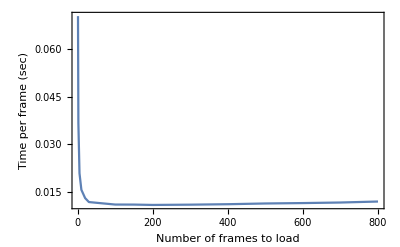

```mathematica
timesPerFrame = Transpose@ {times[[;;,2]] ,  times [[;;,1]]/times [[;;,2]] };
ListPlot[
timesPerFrame, 
Joined-> True, 
AxesOrigin->{0,0},
Frame-> True,
FrameLabel->{"Number of frames to load", "Time per frame (sec)"}, PlotRange->All]
```